Cloudiness

```mathematica
F[s_,t_] = (3-(1+(s-0.2)^2)*Cos[t]^2)/3
```

1/3 (3-(1+(-0.2+s)^2) Cos[t]^2)

```mathematica
Plot3D[F[s,t],{s,-0.4,0.4},{t,-π/2,π/2},PlotLabel->"Average Cloudiness",AxesLabel->{s,t}]
```

-Graphics3D-

```mathematica
Plot3D[F[s,t],{s,-0.4,0.4},{t,-π/2,π/2}, PlotLabel->"Average Cloudiness",AxesLabel->{"Angle from the sun to the plane of the equator at noon", "Angle proportional to the time of day"}]
```

2

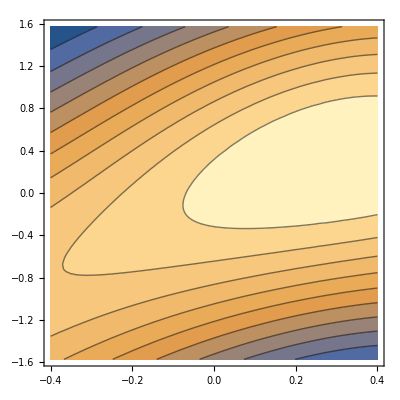

```mathematica
W[s_,u_] = 1+(1+0.65s-1.2s^2-0.4s^3+0.35s^4)*Cos[u]+(1.4s-0.4s^2-1.5s^3-0.35s^4)*Sin[u];
WContours = ContourPlot[W[s,u],{s,-0.4,0.4},{u,-π/2,π/2},Contours->10]
```

```mathematica
D[W[s,u],s]
```

(0.65-2.4 s-1.2 s^2+1.4 s^3) Cos[u]+(1.4-0.8 s-4.5 s^2-1.4 s^3) Sin[u]

```mathematica
Du = D[W[s,u],u];
FindRoot[D[W[s,u],s],{{s,0.3},{u,0}}]
```

FindRoot::nveq: The number of equations does not match the number of variables in FindRoot[∂_s W[s,u],{{s,0.3},{u,0}}].

```mathematica
GW[s_,u_]=Grad[W[s,u],{s,u}]
```

{(0.65-2.4 s-1.2 s^2+1.4 s^3) Cos[u]+(1.4-0.8 s-4.5 s^2-1.4 s^3) Sin[u],(1.4 s-0.4 s^2-1.5 s^3-0.35 s^4) Cos[u]-(1+0.65 s-1.2 s^2-0.4 s^3+0.35 s^4) Sin[u]}

```mathematica
FindRoot[GW[s,u],{{s,0.3},{u,0}}]
```

{s→0.32402,u→0.320456}

```mathematica
DSS[s_,u_]=D[D[W[s,u],s],s];
DUU[s_,u_]=D[D[W[s,u],u],u];
DSU[s_,u_]=D[D[W[s,u],s],u];
Diff[s_,u_] = DSS[s,u] * DUU[s,u] - DSU[s,u]^2;
Diff[0.32402,0.320456]
DSS[0.32402,0.320456]
```

3.99694

```mathematica
-3.906868907086583
W[0.32402,0.320456]
```

-3.90687

2.13253

Crit Point = {s→0.32402,u→0.320456}, 
Differential at point = 3.99694
DXX at point = -3.9068689
Power Generated = 2.13253

```mathematica
Plot3D[W[s,u],{s,-.4,.4},{u,-π/2,π/2}]
```

-Graphics3D-

```mathematica
d1[u_] = D[W[0.4,u],u];
d2[u_] = D[W[-0.4,u],u];
d3[s_]= D[W[s,π/2],s];
d4[s_]=D[W[s,-π/2],s]
```

-1.4+0.8 s+4.5 s^2+1.4 s^3

```mathematica
FindRoot[{d1[u]},{u,0}]
```

{u→0.356083}

^^ is a maximum ?????

```mathematica
FindRoot[{d2[u]},{u,0}]
```

{u→-0.744689}

^^ is a maximum ?????

```mathematica
FindRoot[{d3[s]},{s,0}]
```

{s→0.450206}

^^  Out of domain

```mathematica
FindRoot[{d4[s]},{s,0.5}]
```

{s→0.450206}

^^ Out of domain

## Part 4

### A

Point (0.4 , 0.356083)

```mathematica
W[0.4,0.356083]
```

2.12173

Point (-0.4 , -0.744689)

```mathematica
W[-0.4,-0.744689]
```

1.79228

Point(-0.4, -π/2)

```mathematica
W[-0.4,-π/2]
```

1.53696

Point(-0.4, π/2)     GLOBAL MINIMUM for the given domain

```mathematica
W[-0.4,π/2]
```

0.46304

Point(0.4, -π/2)

```mathematica
W[0.4,-π/2]
```

0.60896

Point(0.4, π/2)

```mathematica
W[0.4,π/2]
```

1.39104

### B

The critical point from part 2 is the global maximum

Part 5

The panel will absorb the most light when s = 0.32402 rad ~= 18.56 Degrees
there for the season that will collect the most solar energy is the summer, the days that collect the most energy are when s is 4.5 degrees off of the 23 at the summer solstice( before the solstice AND after the solstice)

Part 6

```mathematica
svals = Table[s,{s,-0.4,0.4,0.02}];
```

```mathematica
uvals = Table[FindRoot[D[W[s,u],u],{u,0}],{s,-.4,0.4,0.02}];
```

```mathematica
coords = Table[{svals[[i]],u}/.uvals[[i]],{i,Length[svals]}];
```

```mathematica
IdealPointsPlot = ListPlot[coords,PlotStyle->Red];
```

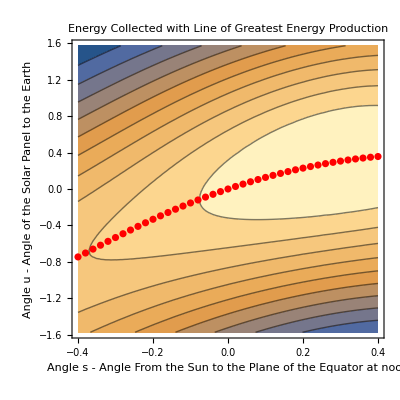

```mathematica
Show[{WContours,IdealPointsPlot},FrameLabel-> {"Angle s - Angle From the Sun to the Plane of the Equator at noon"," Angle u - Angle of the Solar Panel to the Earth"},PlotLabel->" Energy Collected with Line of Greatest Energy Production"]
```

Makes sense because it follows the ride and probably something about gradient

Part 7

If the solar panels need to be replaced then they should be replaced about the winter solstice because the greatest energy production around s = -0.4 is the least of the entire year.  One should start the replacements before the winter solstice and finish after the solstice making the time before and after equal to minimize the amount of energy lost.